```mathematica
$Assumptions=n>1&&n∈Integers&&β>0&&β<1&&α>1
```

n>1&&n∈ℤ&&β>0&&β<1&&α>1

```mathematica
∫_-1^1 Abs[t]^α/(√(1-t^2))ⅆt
```

(√π Gamma[(1+α)/2])/Gamma[1+α/2]

```mathematica
ChebyshevT[10,t]
```

-1+50 t^2-400 t^4+1120 t^6-1280 t^8+512 t^10

```mathematica
∫_-1^1 Abs[t]^α/(√(1-t^2))ChebyshevT[2,t]ⅆt
```

(√π α Gamma[(1+α)/2])/(2 Gamma[2+α/2])

```mathematica
∫_-1^1 Abs[t]^α/(√(1-t^2))ⅆt
```

(√π Gamma[(1+α)/2])/Gamma[1+α/2]

```mathematica
(*попытка явно упростить коэффициент фурье для функции*)
```

```mathematica
FullSimplify[n/2∑_(k=0)^n (-1)^k 2^(2(n-k))*(√π Gamma[(1+α)/2+n-k])/Gamma[1+α/2+n-k]*((2n-k-1)!)/(k!(2n-2k)!)]
```

1/2 n ∑_(k=0)^n ((-1)^k 2^(2 (-k+n)) √π (-1-k+2 n)! Gamma[-k+n+(1+α)/2])/(k! (-2 k+2 n)! Gamma[1-k+n+α/2])

```mathematica
Asymptotic[2^(2(n-k))*(√π Gamma[(1+α)/2+n-k])/Gamma[1+α/2+n-k]*((2n-k-1)!)/(k!(2n-2k)!)/.k-> β*n,n-> ∞]
```

Asymptotic[(2^(2 (n-n β)) √π (-1+2 n-n β)! Gamma[n+(1+α)/2-n β])/((n β)! (2 n-2 n β)! Gamma[1+n+α/2-n β]),n→∞]

```mathematica
Normal[FullSimplify[Series[(2^(2 (n-n β)) √π (-1+2 n-n β)! Gamma[n+(1+α)/2-n β])/((n β)! (2 n-2 n β)! Gamma[1+n+α/2-n β]),{n,∞,2}]]]
```

-ⅇ^(n (2 (-1+β) Log[1-β]-(-2+β) Log[2-β]-β Log[β]))/(2 n^2 (-1+β) √(-(-2+β) β))

```mathematica
∫_0^1 ⅇ^(n (2 (-1+β) Log[1-β]-(-2+β) Log[2-β]-β Log[β]))/(2 n^2 (-1+β) √(-(-2+β) β))ⅆβ
```

∫_0^1 ⅇ^(n (2 (-1+β) Log[1-β]-(-2+β) Log[2-β]-β Log[β]))/(2 n^2 (-1+β) √((2-β) β))ⅆβ

```mathematica
∫_(1/n)^(1-1/n) (ⅇ^(n (2 (-1+β) Log[1-β]-(-2+β) Log[2-β]-β Log[β]))/(2 n^2 (-1+β) √((2-β) β)))ⅆβ
```

∫_(1/n)^(1-1/n) (ⅇ^(n (2 (-1+β) Log[1-β]-(-2+β) Log[2-β]-β Log[β]))/(2 n^2 (-1+β) √((2-β) β)))ⅆβ

```mathematica
∫_-1^1 Abs[t]^α/(√(1-t^2))ChebyshevT[т,t]ⅆt
```

∫_-1^1 (Abs[t]^α ChebyshevT[т,t])/(√(1-t^2))ⅆt

```mathematica
ChebyshevT[3,t]
```

-3 t+4 t^3

```mathematica
list=Table[NIntegrate[Abs[t]^(4/3)/(√(1-t^2))*ChebyshevT[2i,t],{t,-1,1}],{i,1,10}]
```

{0.728595,-0.0910744,0.033118,-0.016559,0.00974058,-0.00633138,0.00440444,-0.00321863,0.00244172,-0.00190759}

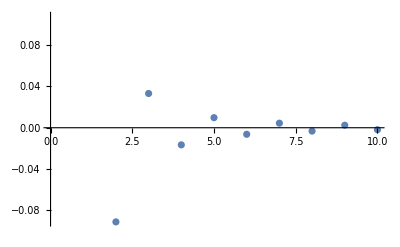

```mathematica
ListPlot[list]
```

```mathematica
ChebAppr[n_,t_]:=1/π NIntegrate[Abs[x]^(4/3)/(√(1-x^2))*ChebyshevT[0,x],{x,-1,1}]*ChebyshevT[0,t]+2/π*∑_(i=1)^n (NIntegrate[Abs[x]^(4/3)/(√(1-x^2))*ChebyshevT[2i,x],{x,-1,1}])*ChebyshevT[2i,t]
```

```mathematica
LegAppr[n_,t_]:=∑_(i=0)^n ((2i+1/2)NIntegrate[Abs[x]^(4/3)*LegendreP[2i,x],{x,-1,1}])*LegendreP[2i,t]
```

```mathematica
2^(2i)∑_(q=0)^(2i)
```

```mathematica
BAppr[n_,t_]:=∑_(k=0)^n ((k/n)^(4/3)BernsteinBasis[n,k,t])
```

```mathematica
BAppr1[n_,t_]:=∑_(k=0)^n ((k/n)^(2/3)BernsteinBasis[n,k,t^2])
```

```mathematica
LegAppr[10,t]
```

0.428571+0.32967 (-1+3 t^2)-0.015616 (3-30 t^2+35 t^4)+0.00360902 (-5+105 t^2-315 t^4+231 t^6)-0.000266423 (35-1260 t^2+6930 t^4-12012 t^6+6435 t^8)+0.0000889488 (-63+3465 t^2-30030 t^4+90090 t^6-109395 t^8+46189 t^10)-0.0000160068 (231-18018 t^2+225225 t^4-1021020 t^6+2078505 t^8-1939938 t^10+676039 t^12)+6.063×10^-6 (-429+45045 t^2-765765 t^4+4849845 t^6-14549535 t^8+22309287 t^10-16900975 t^12+5014575 t^14)-2.97923×10^-7 (6435-875160 t^2+19399380 t^4-162954792 t^6+669278610 t^8-1487285800 t^10+1825305300 t^12-1163381400 t^14+300540195 t^16)+1.20472×10^-7 (-12155+2078505 t^2-58198140 t^4+624660036 t^6-3346393050 t^8+10039179150 t^10-17644617900 t^12+18032411700 t^14-9917826435 t^16+2268783825 t^18)-2.49059×10^-8 (46189-9699690 t^2+334639305 t^4-4461857400 t^6+30117537450 t^8-116454478140 t^10+273491577450 t^12-396713057400 t^14+347123925225 t^16-167890003050 t^18+34461632205 t^20)

```mathematica
N[ChebAppr[2,t]]
```

0.579798+0.63662 (0.728595 (-1.+2. t^2)-0.0910744 (1.-8. t^2+8. t^4))

```mathematica
BernsteinBasis[2,2,0.5]
```

0.25

```mathematica
BAppr[2,0.5]
```

0.448425

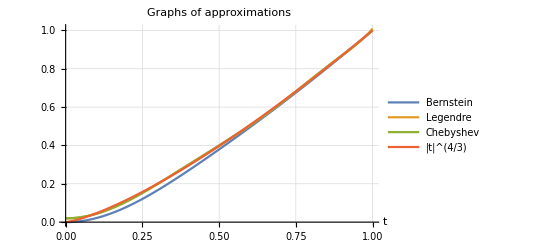

```mathematica
polApprs=Plot[{BAppr1[10,t],LegAppr[5,t],ChebAppr[5,t],t^(4/3)},{t,0,1},GridLines->Automatic,PlotLegends->{"Bernstein", "Legendre", "Chebyshev", "|t|^(4/3)"}, PlotLabel->"Graphs of approximations",AxesLabel->{"t",""}]
```

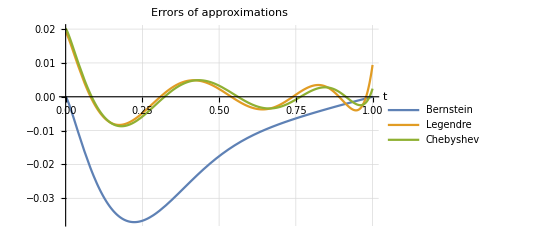

```mathematica
polErr=Plot[{BAppr1[10,t]-t^(4/3),LegAppr[5,t]-t^(4/3),ChebAppr[5,t]-t^(4/3)},{t,0,1},GridLines->Automatic,PlotLegends->{"Bernstein", "Legendre", "Chebyshev"}, PlotLabel->"Errors of approximations",AxesLabel->{"t",""}]
```

```mathematica
Export["N:\\DGAP\\major\\НИР\\Fractional_power\\pol_apprs.png",polApprs]
Export["N:\\DGAP\\major\\НИР\\Fractional_power\\pol_errors.png", polErr]
```

N:\DGAP\major\НИР\Fractional_power\pol_apprs.png

N:\DGAP\major\НИР\Fractional_power\pol_errors.png

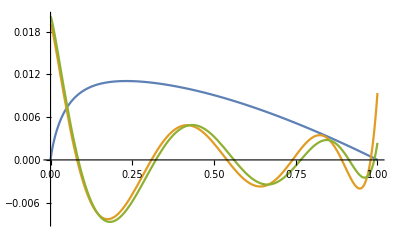

```mathematica
Plot[{BAppr[10,t]-t^(4/3),LegAppr[5,t]-t^(4/3),ChebAppr[5,t]-t^(4/3)},{t,0,1}]
```

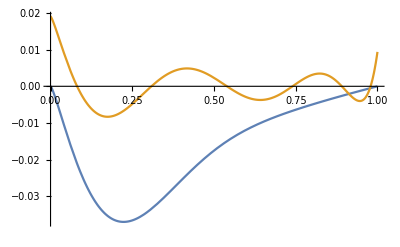

```mathematica
Plot[{BAppr1[10,t]-t^(4/3),LegAppr[5,t]-t^(4/3),ChebAppr[5,t]-t^(4/3)},{t,0,1}]
```

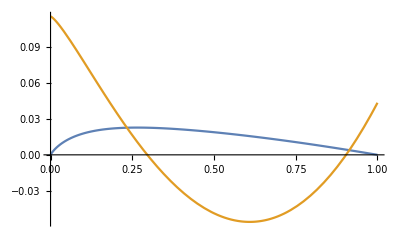

```mathematica
Plot[{BAppr[5,t]-t^(4/3),ChebAppr[1,t]-t^(4/3)},{t,0,1}]
```

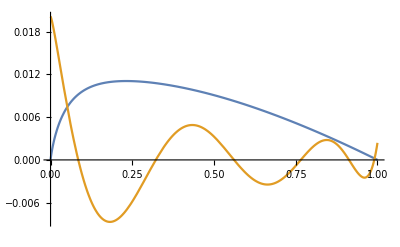

```mathematica
Plot[{BAppr[10,t]-t^(4/3),ChebAppr[5,t]-t^(4/3)},{t,0,1}]
```

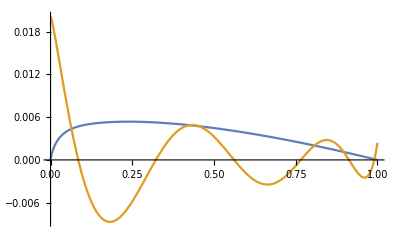

```mathematica
Plot[{BAppr[20,t]-t^(4/3),ChebAppr[5,t]-t^(4/3)},{t,0,1}]
```

```mathematica
Plot[{BAppr[20,t]-t^(4/3),ChebAppr[10,t]-t^(4/3)},{t,0,1}]
```

$Aborted

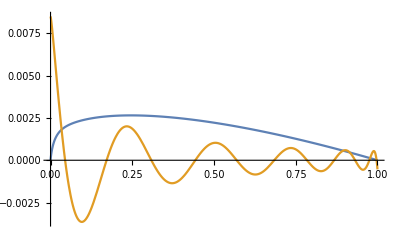

```mathematica
Plot[{BAppr[40,t]-t^(4/3),ChebAppr[10,t]-t^(4/3)},{t,0,1}]
```

```mathematica
Plot[{BAppr[10,t]-t^(4/3),ChebAppr[5,t]-t^(4/3)},{t,0,1}]
```

```mathematica
ChebApprRed[n_,t_]:=1/π NIntegrate[Abs[x]^(1/3)/(√(1-x^2))*ChebyshevT[0,x],{x,-1,1}]*ChebyshevT[0,t]+2/π*∑_(i=1)^n (NIntegrate[Abs[x]^(1/3)/(√(1-x^2))*ChebyshevT[2i,x],{x,-1,1}])*ChebyshevT[2i,t]
```

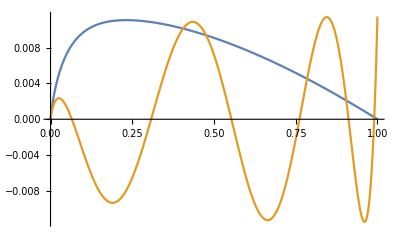

```mathematica
Plot[{BAppr[10,t]-t^(4/3),t*ChebApprRed[5,t]-t^(4/3)},{t,0,1}]
```

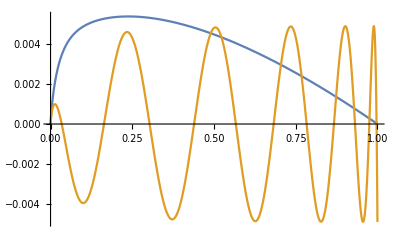

```mathematica
Plot[{BAppr[20,t]-t^(4/3),t*ChebApprRed[10,t]-t^(4/3)},{t,0,1}]
```

```mathematica
listB=Table[NIntegrate[t*(BAppr[2n,t]-t^(4/3)),{t,0,1}],{n,1,10}]
```

{0.0161417,0.00770706,0.00502353,0.00372016,0.00295242,0.00244696,0.00208914,0.00182257,0.00161631,0.00145198}

```mathematica
listCh=Table[NIntegrate[t*(ChebAppr[n,t]),{t,0,1},AccuracyGoal->8],{n,1,10}]-Table[NIntegrate[t^(7/3),{t,0,1}],{n,1,10}]
```

{-0.0101012,-0.00043789,-0.00043789,-0.0000864972,-0.0000864972,-0.0000289161,-0.0000289161,-0.0000126539,-0.0000126539,-6.52051×10^-6}

```mathematica
listL=Table[NIntegrate[t*(LegAppr[n,t]),{t,0,1},AccuracyGoal->8],{n,1,10}]-Table[NIntegrate[t^(7/3),{t,0,1}],{n,1,10}]
```

{-0.0032967,-0.000694043,-0.000242915,-0.000109704,-0.000057817,-0.0000338067,-0.0000213018,-0.0000142013,-9.89439×10^-6,-7.14228×10^-6}

```mathematica
ListB
```

ListB

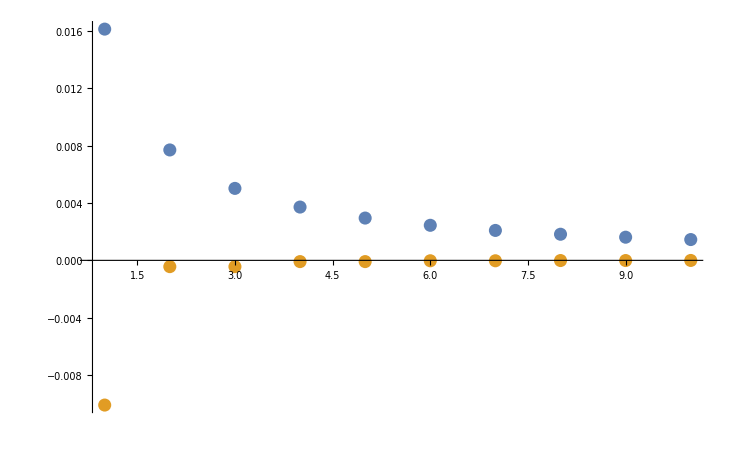

```mathematica
ListPlot[{listB,listCh},PlotRange->All]
```

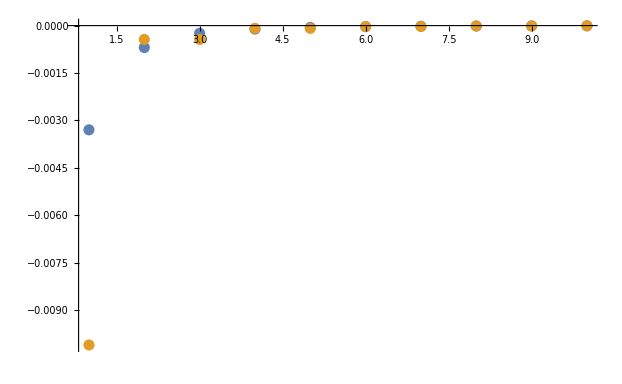

```mathematica
ListPlot[{listL⟦1;;⟧,listCh⟦1;;⟧},PlotRange->All]
```

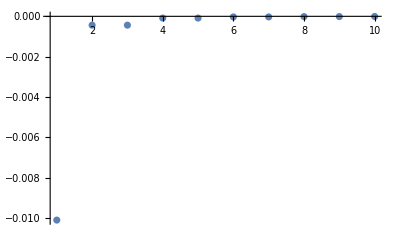

```mathematica
ListPlot[{listCh},PlotRange->All]
```

```mathematica
list1B=Table[NIntegrate[(BAppr[2n,t]-t^(4/3)),{t,0,1}],{n,1,10}]
```

{0.0370453,0.0185807,0.0123249,0.0092016,0.0073346,0.00609461,0.00521186,0.00455173,0.00403959,0.00363077}

```mathematica
list1Ch=Table[NIntegrate[(ChebAppr[n,t]),{t,0,1},AccuracyGoal->8],{n,1,10}]-Table[NIntegrate[t^(4/3),{t,0,1}],{n,1,10}]
```

{-0.0033865,0.00047882,-0.000123567,0.0000437627,-0.0000188741,9.3125×10^-6,-5.06673×10^-6,2.96872×10^-6,-1.8438×10^-6,1.19983×10^-6}

```mathematica
list1L=Table[NIntegrate[(LegAppr[n,t]),{t,0,1},AccuracyGoal->8],{n,1,10}]-Table[NIntegrate[t^(4/3),{t,0,1}],{n,1,10}]
```

{5.55112×10^-16,4.996×10^-16,5.55112×10^-16,6.10623×10^-16,4.44089×10^-16,4.44089×10^-16,5.55112×10^-16,4.44089×10^-16,6.66134×10^-16,-1.86517×10^-14}

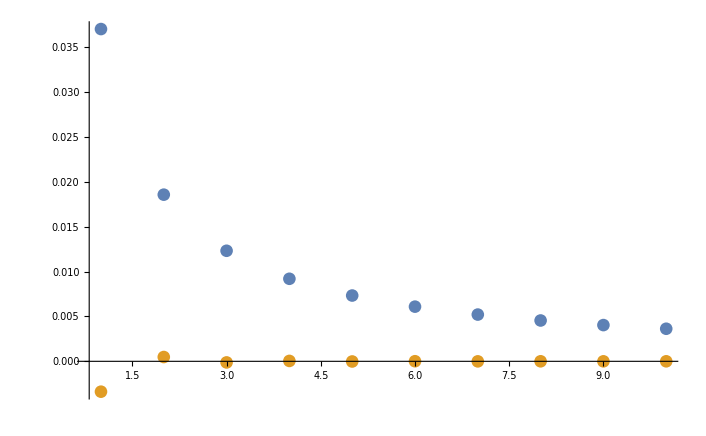

```mathematica
ListPlot[{list1B,list1Ch},PlotRange->All]
```

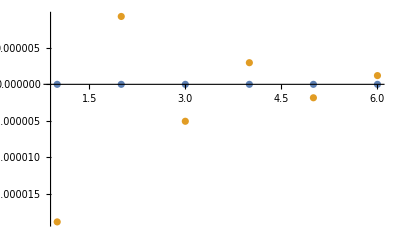

```mathematica
ListPlot[{list1L⟦5;;⟧,list1Ch⟦5;;⟧},PlotRange->All]
```

```mathematica
list2Ch=Table[NIntegrate[(1+t^4+55 t^3)*(ChebAppr[n,t]),{t,0,1},AccuracyGoal->8],{n,1,15}]-Table[NIntegrate[t^(16/3)+55 t^(13/3)+t^(4/3),{t,0,1}],{n,1,15}]
```

{-0.219922,0.052813,-0.00688269,0.00316113,-0.00103371,0.00060886,-0.000277638,0.000186051,-0.000101342,0.0000735087,-0.0000447413,0.0000342532,-0.0000224824,0.0000179121,-0.0000124051}

```mathematica
list2B=Table[NIntegrate[(1+t^4+55 t^3)*(BAppr[2n,t]),{t,0,1},AccuracyGoal->8],{n,1,10}]-Table[NIntegrate[t^(16/3)+55 t^(13/3)+t^(4/3),{t,0,1}],{n,1,10}]
```

{0.35019,0.16313,0.106034,0.0785485,0.062386,0.051743,0.0442036,0.0385825,0.03423,0.0307601}

```mathematica
list2L=Table[NIntegrate[(1+t^4+55 t^3)*(LegAppr[n,t]),{t,0,1},AccuracyGoal->8],{n,1,15}]-Table[NIntegrate[t^(16/3)+55 t^(13/3)+t^(4/3),{t,0,1}],{n,1,15}]
```

{0.116497,0.00596447,0.00100207,0.000269406,0.0000946849,0.0000396614,0.0000188198,9.80766×10^-6,5.5008×10^-6,3.27484×10^-6,2.04941×10^-6,1.33881×10^-6,9.08515×10^-7,6.38649×10^-7,4.69874×10^-7}

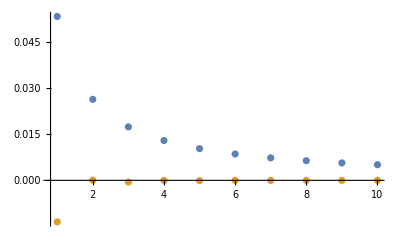

```mathematica
ListPlot[{list2B,list2Ch},PlotRange->All]
```

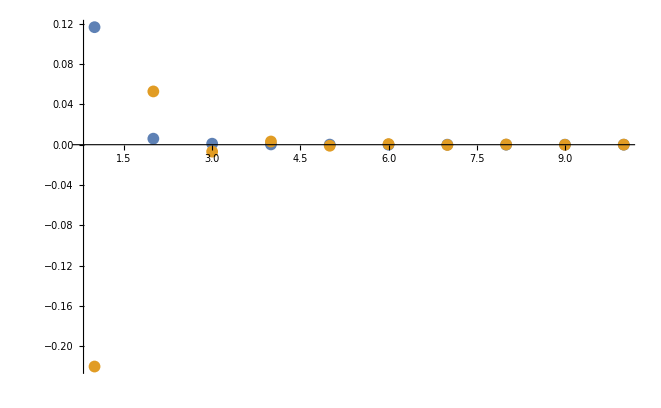

```mathematica
ListPlot[{list2L⟦1;;10⟧,list2Ch⟦1;;10⟧},PlotRange->All]
```

```mathematica
NIntegrate[(1+t^2)*(BAppr[30,t]-t^(4/3)),{t,0,1},AccuracyGoal->8]
```

0.00292323

```mathematica
ChebyshevT[4,t]
```

1-8 t^2+8 t^4

```mathematica
ChebyshevT[2,t]
```

-1+2 t^2

```mathematica
ChebyshevT[0,t]
```

1

```mathematica
LegendreP[2,t]
```

1/2 (-1+3 t^2)

```mathematica
Factor[Det[({{1, q, q}, {q, 1, q}, {q, q, 1}})]]
```

(-1+q)^2 (1+2 q)

```mathematica
Factor[Inverse[({{1, q, q}, {q, 1, q}, {q, q, 1}})]]//MatrixForm
```

(-(1+q)/((-1+q) (1+2 q)) | q/((-1+q) (1+2 q)) | q/((-1+q) (1+2 q))
q/((-1+q) (1+2 q)) | -(1+q)/((-1+q) (1+2 q)) | q/((-1+q) (1+2 q))
q/((-1+q) (1+2 q)) | q/((-1+q) (1+2 q)) | -(1+q)/((-1+q) (1+2 q)))

```mathematica
Factor[Det[({{1, q, q, q}, {q, 1, q, q}, {q, q, 1, q}, {q, q, q, 1}})]]
```

-(-1+q)^3 (1+3 q)

```mathematica
Factor[Inverse[({{1, q, q, q}, {q, 1, q, q}, {q, q, 1, q}, {q, q, q, 1}})]]//MatrixForm
```

(-(1+2 q)/((-1+q) (1+3 q)) | q/((-1+q) (1+3 q)) | q/((-1+q) (1+3 q)) | q/((-1+q) (1+3 q))
q/((-1+q) (1+3 q)) | -(1+2 q)/((-1+q) (1+3 q)) | q/((-1+q) (1+3 q)) | q/((-1+q) (1+3 q))
q/((-1+q) (1+3 q)) | q/((-1+q) (1+3 q)) | -(1+2 q)/((-1+q) (1+3 q)) | q/((-1+q) (1+3 q))
q/((-1+q) (1+3 q)) | q/((-1+q) (1+3 q)) | q/((-1+q) (1+3 q)) | -(1+2 q)/((-1+q) (1+3 q)))

```mathematica
f=∑_(n=1)^∞ Gamma[n/2+2n/3]/Gamma[3n/2] z^n
```

1/(4776408 √π)(1061424 √π z^2 Gamma[1/3] HypergeometricPFQ[{10/21,13/21,16/21,19/21,22/21,25/21},{4/9,5/9,2/3,7/9,8/9,10/9,11/9},(823543 z^6)/387420489]+432432 √π z^4 Gamma[2/3] HypergeometricPFQ[{17/21,20/21,23/21,26/21,29/21,32/21},{7/9,8/9,10/9,11/9,4/3,13/9,14/9},(823543 z^6)/387420489]+1592136 z Gamma[1/6] HypergeometricPFQ[{13/42,19/42,25/42,31/42,37/42,1,43/42},{5/18,7/18,1/2,11/18,13/18,5/6,17/18,19/18},(823543 z^6)/387420489]+1364688 √π z^3 HypergeometricPFQ[{9/14,11/14,13/14,1,15/14,17/14,19/14},{11/18,13/18,5/6,17/18,19/18,7/6,23/18,25/18},(823543 z^6)/387420489]+362848 z^5 Gamma[5/6] HypergeometricPFQ[{41/42,1,47/42,53/42,59/42,65/42,71/42},{17/18,19/18,7/6,23/18,25/18,3/2,29/18,31/18},(823543 z^6)/387420489]+85293 √π z^6 HypergeometricPFQ[{1,8/7,9/7,10/7,11/7,12/7,13/7},{10/9,11/9,4/3,13/9,14/9,5/3,16/9,17/9},(823543 z^6)/387420489])

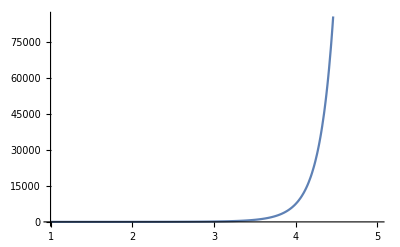

```mathematica
Plot[f/.z-> -z,{z,1,5}]
```

```mathematica
Asymptotic[Gamma[n/2+2n/3]/Gamma[3n/2],n->∞]
```

$Aborted

```mathematica
∑_(n=1)^∞ n^(1/2)/Gamma[2n/3] z^n
```

∑_(n=1)^∞ (√n z^n)/Gamma[(2 n)/3]

```mathematica
∑_(n=1)^∞ Gamma[n/3]/Gamma[n+1] z^n
```

∑_(n=1)^∞ (z^n Gamma[n/3])/Gamma[1+n]

```mathematica
∑_(n=1)^∞ 1/Gamma[2n/3] z^n
```

(z Gamma[1/3] HypergeometricPFQ[{1},{1/3,5/6},z^3/4]+3 z^2 Gamma[2/3] HypergeometricPFQ[{1},{2/3,7/6},z^3/4]+z^(3/2) Gamma[1/3] Gamma[2/3] Sinh[z^(3/2)])/(Gamma[1/3] Gamma[2/3])

```mathematica
∑_(n=1)^∞ Gamma[2n/3]/Gamma[n](-z)^n
```

1/6 (-6 z Gamma[2/3] Hypergeometric1F1[5/6,2/3,-(4 z^3)/27]+2 z^2 Gamma[1/3] Hypergeometric1F1[7/6,4/3,-(4 z^3)/27]-3 z^3 HypergeometricPFQ[{1,3/2},{4/3,5/3},-(4 z^3)/27])

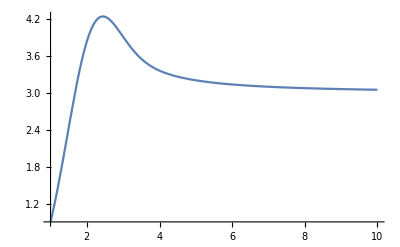

```mathematica
Plot[z^3 HypergeometricPFQ[{1,3/2},{4/3,5/3},-(4 z^3)/27],{z,1,10},PlotRange->All]
```

```mathematica
(*разберись аккуратно с вещ и мнимыми частями на разных ветках!!!*)
```

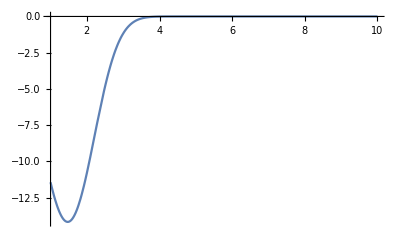

```mathematica
Plot[-6 z Gamma[2/3] Hypergeometric1F1[5/6,2/3,-(4 z^3)/27]-2 z^2 Gamma[1/3] Hypergeometric1F1[7/6,4/3,-(4 z^3)/27],{z,1,10}]
```

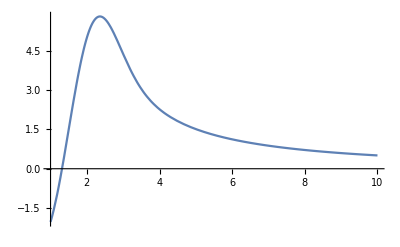

```mathematica
Plot[-6 z Gamma[2/3] Hypergeometric1F1[5/6,2/3,-(4 z^3)/27]+2 z^2 Gamma[1/3] Hypergeometric1F1[7/6,4/3,-(4 z^3)/27],{z,1,10}]
```

```mathematica
Limit[-6 z Gamma[2/3] Hypergeometric1F1[5/6,2/3,-(4 z^3)/27]+2 z^2 Gamma[1/3] Hypergeometric1F1[7/6,4/3,-(4 z^3)/27],z-> ∞]
```

0

```mathematica
Asymptotic[-6 z Gamma[2/3] Hypergeometric1F1[5/6,2/3,-(4 z^3)/27]+2 z^2 Gamma[1/3] Hypergeometric1F1[7/6,4/3,-(4 z^3)/27],z-> ∞]
```

-(2 (-1)^(1/6) 2^(1/3) √3 ⅇ^(-(4 z^3)/27) z^(3/2) Gamma[2/3]^2)/Gamma[5/6]-((-1)^(5/6) 2^(2/3) √3 ⅇ^(-(4 z^3)/27) z^(3/2) Gamma[1/3] Gamma[4/3])/Gamma[7/6]

```mathematica
Asymptotic[z^3 HypergeometricPFQ[{1,3/2},{4/3,5/3},-(4 z^3)/27],z-> ∞]
```

(2 √3 π)/(Gamma[1/3] Gamma[2/3])

```mathematica
(*Нужно брать вещ часть, мнимая = погрешность и должна сократиться!!!
видимо, следующее правильно, потому что через 0 проходит, как и должно*)
```

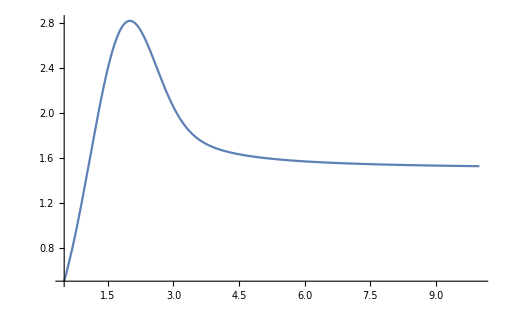

```mathematica
Plot[-1/6 ((-6 z Gamma[2/3] Hypergeometric1F1[5/6,2/3,-(4 z^3)/27]-2 z^2 Gamma[1/3] Hypergeometric1F1[7/6,4/3,-(4 z^3)/27])Cos[π/3]-3 z^3 HypergeometricPFQ[{1,3/2},{4/3,5/3},-(4 z^3)/27]),{z,0.5,10},PlotRange->All]
```

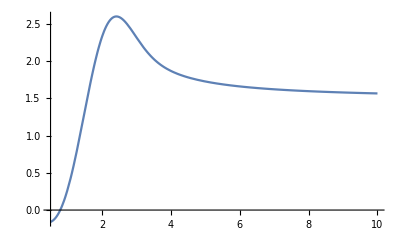

```mathematica
Plot[-1/6 ((-6 z Gamma[2/3] Hypergeometric1F1[5/6,2/3,-(4 z^3)/27]+2 z^2 Gamma[1/3] Hypergeometric1F1[7/6,4/3,-(4 z^3)/27])Cos[2π/3]-3 z^3 HypergeometricPFQ[{1,3/2},{4/3,5/3},-(4 z^3)/27]),{z,0.5,10},PlotRange->All]
```